```mathematica
σx=0.5;
σy=0.25;
f[x_,y_,b_] = (1+b x)Exp[-x^2/σx]Exp[-y^2/σy];
g[x_,σ_,x0_,b_] =  (1+b x)Exp[-(x-x0)^2/(2σ)];
gserie1[x_] =  (1+b x)*(1+(-(x-x0)^2/σ));
gserie2[x_,σ_,x0_,b_] =  (1+b x)*(1+(-(x-x0)^2/σ)+1/2(-(x-x0)^2/σ)^2);
gserie3[x_,σ_,x0_,b_] =  (1+b x)*(1+(-(x-x0)^2/σ)+1/2(-(x-x0)^2/σ)^2+1/6(-(x-x0)^2/σ)^3);
(*maximo[x_,σ_,x0_,b_]=*)
FullSimplify[Solve[D[g[x,σ,x0,a]==0,x],x]][[1,1,2]]
Solve[FullSimplify[Solve[D[g[x,σ,x0,a]==0,x],x]][[1,1,2]]==y,a][[1,1,2]]

FullSimplify[Solve[D[g[x,σ,x0,a]==0,x],x]][[2,1,2]]
Solve[FullSimplify[Solve[D[g[x,σ,x0,a]==0,x],x]][[2,1,2]]==y,a][[1,1,2]]
```

-(1-a x0+√((1+a x0)^2+4 a^2 σ))/(2 a)

(-x0+y)/(x0 y-y^2+σ)

(-1+a x0+√((1+a x0)^2+4 a^2 σ))/(2 a)

(-x0+y)/(x0 y-y^2+σ)

-Graphics3D-

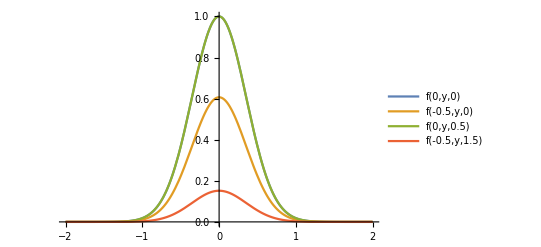

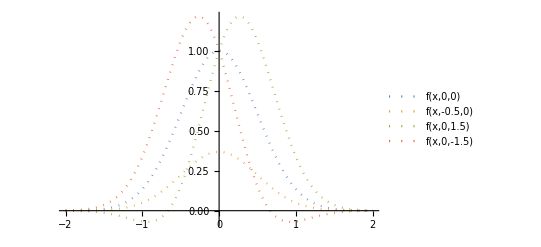

```mathematica
Plot3D[f[x,y,1.5],{x,-1,1},{y,-1,1}]
Plot[{f[0,y,0],f[-0.5,y,0],f[0,y,0.5],f[-0.5,y,1.5]},{y,-2,2},PlotLegends->"Expressions"]
Plot[{f[x,0,0],f[x,-0.5,0],f[x,0,1.5],f[x,0,-1.5]},{x,-2,2},PlotStyle->Dotted,PlotLegends->"Expressions"]
```

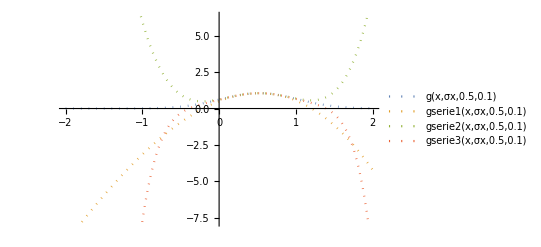

```mathematica
Plot[{g[x,σx,0.5,0.1],gserie1[x,σx,0.5,0.1],gserie2[x,σx,0.5,0.1],gserie3[x,σx,0.5,0.1]},{x,-2,2},PlotStyle->Dotted,PlotLegends->"Expressions"]
```